# Compare high-frequency expansions and numerical results for the Spin-Weighted Spheroidal Eigenvalue and Eigenfunction

For details see “High-order asymptotics for the Spin-Weighted Spheroidal Equation at large real frequency”, M. Casals, A. C. Ottewill, N. Warburton, arXiv:1810.00432

```mathematica
$PlotTheme="Detailed";
```

Load the SpinWeightedSpheoridalHarmonics Package which can be obtained from bhptoolkit.org

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

## Eigenvalues for large real frequency

```mathematica
maxOrder=30;
s=2;
l=2;
m=2;
```

```mathematica
λHF=Series[SpinWeightedSpheroidalEigenvalue[s,l,m,γ],{γ,∞,maxOrder}]
```

-6 γ-1+3/(4 γ)-15/(64 γ^3)-3/(16 γ^4)+3/(512 γ^5)+27/(128 γ^6)+5109/(16384 γ^7)+519/(2048 γ^8)+8781/(131072 γ^9)-585/(4096 γ^10)-526611/(2097152 γ^11)-96027/(524288 γ^12)+587283/(16777216 γ^13)+1171233/(4194304 γ^14)+419534925/(1073741824 γ^15)+18248187/(67108864 γ^16)-335708823/(8589934592 γ^17)-395170893/(1073741824 γ^18)-67821141513/(137438953472 γ^19)-9826998495/(34359738368 γ^20)+201642365301/(1099511627776 γ^21)+177645378141/(274877906944 γ^22)+27276887972865/(35184372088832 γ^23)+1746181377741/(4398046511104 γ^24)-97983031410591/(281474976710656 γ^25)-18022391804547/(17592186044416 γ^26)-5092816038278091/(4503599627370496 γ^27)-493267808474247/(1125899906842624 γ^28)+27880930799380083/(36028797018963968 γ^29)+15988982395587381/(9007199254740992 γ^30)+O[1/γ]^31

```mathematica
Monitor[λN=Table[{γ,SpinWeightedSpheroidalEigenvalue[s,l,m,γ]},{γ,0,40,0.1`40}],γ];
```

```mathematica
Monitor[Table[diff[n]=Table[{γ,λN[[i,2]]-Normal[Series[λHF,{γ,∞,n}]]}/.γ->λN[[i,1]],{i,2,Length[λN]}],{n,-2,maxOrder}],n];
```

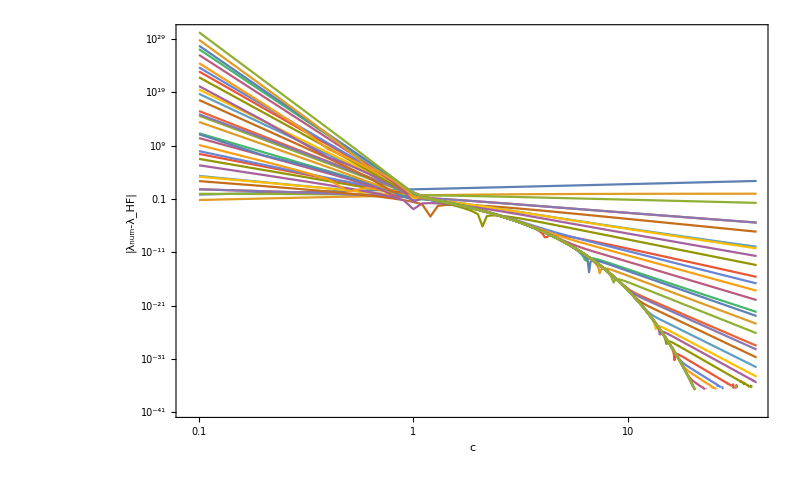

```mathematica
ListLogLogPlot[Table[diff[n],{n,-2,maxOrder}]//Abs,Joined->True,PlotTheme->"Detailed",BaseStyle->25,FrameLabel->{"c","|λ_num-λ_HF|"},ImageSize->800]
```

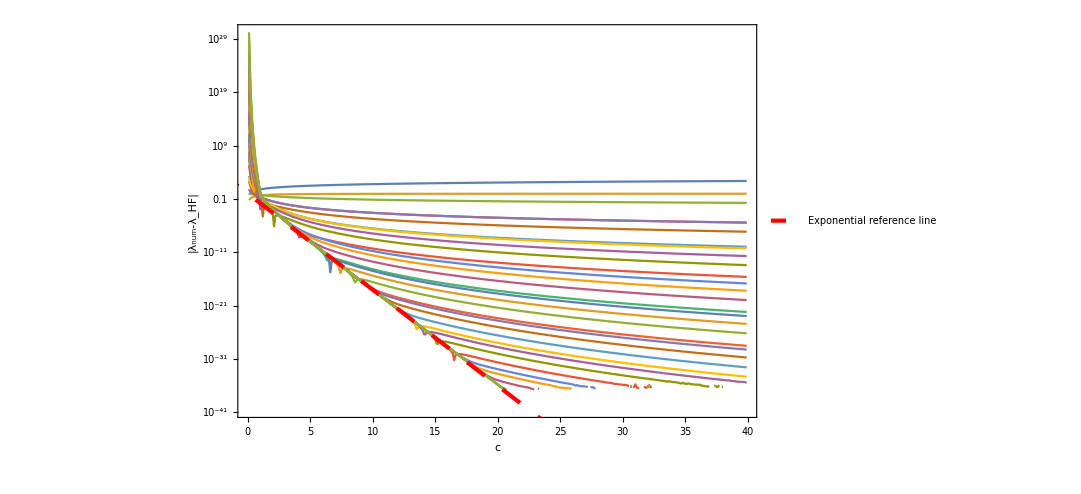

```mathematica
Show[
ListLogPlot[Table[diff[n],{n,-2,maxOrder}]//Abs,Joined->True,PlotTheme->"Detailed",BaseStyle->25,FrameLabel->{"c","|λ_num-λ_HF|"},ImageSize->800],
LogPlot[Exp[-4.15γ],{γ,-5,40},PlotStyle->{Red,Dashing[0.02],AbsoluteThickness[3]},PlotLegends->Placed[LineLegend[{"Exponential reference line"},LabelStyle->20],Scaled[{0.3,0.9}]]]
]
```

## Generate the a_(n,k)’s and A_k’s defined in Eq. (3.12) and Eq. (3.13), respectively

This code is almost identical to that in the package but it returns results in terms of s, l, m, and q.

```mathematica
GenerateAk[s_,l_,m_,q_,order_]:=Module[{slm,z0,aFgen,AFgen,Asgen,δgen,νgen,RecRelgen,n,c,p,Serngen,Ak,ank},
  aFgen[0,_]=0;
  aFgen[0,0]=1;

  AFgen[0]=1;
  AFgen[r_]=AFgen[0]Sum[aFgen[r,k]c^-k,{k,Abs[r], order+1}];
  
  Asgen=Sum[δgen[k]c^-k, {k, 1, order+1}];
  νgen=1/2 (-1+q-s-Abs[m+s]);
  RecRelgen=1/2  (1+n+νgen+Abs[m+s]) (2(1+n+νgen+s)-Abs[m-s]+Abs[m+s])AFgen[n+1]+(-1-m-m^2-2 (n+ νgen)+4 c n-2 (n+νgen)^2-s-m s-2 (n+νgen) s-4 c Asgen-(1+2 n+2 νgen+s) Abs[m+s])AFgen[n] + 1/2  (n+νgen) (2 (n+νgen+s)+Abs[m-s]+Abs[m+s])AFgen[n-1];

  Serngen[nn_]:=Serngen[nn]=Collect[CoefficientList[Normal[Series[RecRelgen/.n->nn,{c, ∞, order+1}]],c^-1],aFgen[_,_]];

  Do[
    δgen[p]=δgen[p]/.Solve[Serngen[0][[p]]==0,δgen[p]][[1]];
    Do[If[k!=0,aFgen[k,p]=aFgen[k,p]/.Solve[Serngen[k][[p]]==0,aFgen[k,p]][[1]]],{k, -p, p}]
  ,{p, 1, order+1}];
 
 Ak = Table[4δgen[k],{k, 2, order+1}];
ank=Table[aFgen[n,k],{k,1,order},{n,-k,k}];

{Ak,ank}

];
```

```mathematica
maxOrder=4;
coeffs=Simplify[GenerateAk[s,l,m,q,maxOrder],Assumptions->{{s,m,q} ∈Reals}];
```

```mathematica
Ak[k_?NumberQ]:=coeffs[[1,k]];
```

```mathematica
Ak[1]
Ak[2]
```

1/8 (-q^3+2 m s^2+q (-1+m^2+2 s^2))

1/64 (-1-m^4-5 q^4+4 s^2+16 m q s^2+m^2 (2+6 q^2+4 s^2)+2 q^2 (-5+6 s^2))

```mathematica
ank[n_,k_]:=If[Abs[n]≤k,coeffs[[2,k,n+k+1]],0];
```

```mathematica
ank[-1,1]
ank[-2,2]
```

1/16 (-1+q+s-Abs[m-s]) (-1+q-s+Abs[m+s])

1/512 (3+m^2-4 q+q^2-4 s-2 m s+2 q s+2 s^2-2 (-2+q+s) Abs[m-s]) (3+m^2-4 q+q^2+4 s+2 m s-2 q s+2 s^2+2 (-2+q-s) Abs[m+s])